## Eigenvalues DQD

```mathematica
Hamiltoniano1={{Subscript[ϵ, L]+Subscript[ϵ, R]+Subscript[e, Z],0,0,0,I*Subscript[t, F]},{0,Subscript[ϵ, L]+Subscript[ϵ, R],0,0,-Subscript[t, n]},{0,0,Subscript[ϵ, L]+Subscript[ϵ, R],0,Subscript[t, n]},{0,0,0,Subscript[ϵ, L]+Subscript[ϵ, R]-Subscript[e, Z],-I*Subscript[t, F]},{-I*Subscript[t, F],-Subscript[t, n],Subscript[t, n],I *Subscript[t, F],2*Subscript[ϵ, R]+u}};
Hamiltoniano2={{-Subscript[e, Z],Subscript[λ, 1],Subscript[λ, 2]},{Subscript[λ, 1],0,Sqrt[2]*τ},{Subscript[λ, 2],Sqrt[2]*τ,ϵ+u}};
MatrixForm[Hamiltoniano1]
MatrixForm[Hamiltoniano2]
ez=1.17;
param={Subscript[λ, 1]->0,Subscript[λ, 2]->Subscript[t, F],τ->Subscript[t, n],Subscript[t, F]->0.1,Subscript[t, n]->0.25,u-> 3000,Subscript[e, Z]->ez,Subscript[ϵ, L]->-ϵ/2,Subscript[ϵ, R]->ϵ/2,ϵ->ϵvar*Subscript[e, Z]-u};
Hamiltoniano1param=Hamiltoniano1//.param;
Hamiltoniano2param=Hamiltoniano2//.param;
```

(e_Z+ϵ_L+ϵ_R | 0 | 0 | 0 | ⅈ t_F
0 | ϵ_L+ϵ_R | 0 | 0 | -t_n
0 | 0 | ϵ_L+ϵ_R | 0 | t_n
0 | 0 | 0 | -e_Z+ϵ_L+ϵ_R | -ⅈ t_F
-ⅈ t_F | -t_n | t_n | ⅈ t_F | u+2 ϵ_R)

(-e_Z | λ_1 | λ_2
λ_1 | 0 | √2 τ
λ_2 | √2 τ | u+ϵ)

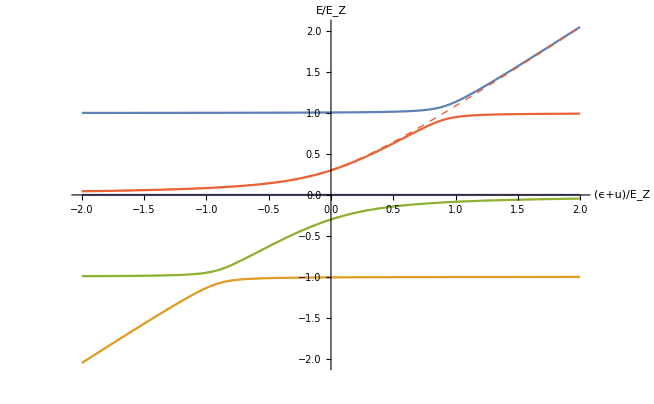

```mathematica
sol1=Eigensystem[Hamiltoniano1param];
energias1=sol1[[1]]/ez;
sol2=Eigensystem[Hamiltoniano2param];
energias2=sol2[[1]]/ez;
Plot[{energias1,energias2},{ϵvar,-2,2},AxesLabel->{"(ϵ+u)/E_Z","E/E_Z"},PlotStyle->{{RGBColor[0.528488, 0.470624, 0.701351]},{RGBColor[0.880722, 0.611041, 0.142051]},{RGBColor[0.560181, 0.691569, 0.194885]},{RGBColor[0.922526, 0.385626, 0.209179]},{RGBColor[0.368417, 0.506779, 0.709798]},{RGBColor[0.880722, 0.611041, 0.142051],Dashed,Thick},{RGBColor[0.560181, 0.691569, 0.194885],Dashed,Thick},{RGBColor[0.922526, 0.385626, 0.209179],Dashed,Thick}}]
```

```mathematica
temp=Simplify[Solve[(Eigenvalues[Hamiltoniano2][[1,1,1]]/. {#1->x,Subscript[λ, 1]->0,Subscript[λ, 2]->0})==0,x]]
```

{{x→1/2 (u+ϵ-√(u^2+2 u ϵ+ϵ^2+8 τ^2))},{x→1/2 (u+ϵ+√(u^2+2 u ϵ+ϵ^2+8 τ^2))},{x→-e_Z}}

```mathematica
Htemp=Hamiltoniano2/. Subscript[λ, 1]->0
```

{{-e_Z,0,λ_2},{0,0,√2 τ},{λ_2,√2 τ,u+ϵ}}

```mathematica
Simplify[Solve[(Eigenvectors[Hamiltoniano2][[1,2]]/. {#1->x,Subscript[λ, 1]->0})==0,x], Assumptions->{u>0, τ>0, Subscript[e, Z]>0, Subscript[λ, 2]>0,ϵ ∈ Reals}]
```

Root::deg: x^3-2 τ^2 e_Z+x^2 (-u-ϵ+e_Z)+x (-2 τ^2-u e_Z-ϵ e_Z-λ_2^2) has fewer than 1 root(s) as a polynomial in #1.

Solve::nsmet: This system cannot be solved with the methods available to Solve.

{}

```mathematica
RootReduce[Denominator[(Eigenvectors[Hamiltoniano2/. {Subscript[λ, 1]->0}][[1,2]])]]
```

Root[#1^3-2 τ^2 e_Z+#1^2 (-u-ϵ+e_Z)+#1 (-2 τ^2-u e_Z-ϵ e_Z-λ_2^2)&,1]

## Eigenvalues TQD

```mathematica
Remove["Global`*"]
```

```mathematica
H={{e1+EZ/2,0,-tN12,-tF12*Exp[I*phase],0,0},{0,e1-EZ/2,-tF12*Exp[I*phase],-tN12,0,0},{-tN12,-tF12*Exp[-I*phase],e2+EZ/2,0,-tN23,-tF23*Exp[I*phase]},{-tF12*Exp[-I*phase],-tN12,0,e2-EZ/2,-tF23*Exp[I*phase],-tN23},{0,0,-tN23,-tF23*Exp[-I*phase],e3+EZ/2,0},{0,0,-tF23*Exp[-I*phase],-tN23,0,e3-EZ/2}};
MatrixForm[H]
```

(e1+EZ/2 | 0 | -tN12 | -ⅇ^(ⅈ phase) tF12 | 0 | 0
0 | e1-EZ/2 | -ⅇ^(ⅈ phase) tF12 | -tN12 | 0 | 0
-tN12 | -ⅇ^(-ⅈ phase) tF12 | e2+EZ/2 | 0 | -tN23 | -ⅇ^(ⅈ phase) tF23
-ⅇ^(-ⅈ phase) tF12 | -tN12 | 0 | e2-EZ/2 | -ⅇ^(ⅈ phase) tF23 | -tN23
0 | 0 | -tN23 | -ⅇ^(-ⅈ phase) tF23 | e3+EZ/2 | 0
0 | 0 | -ⅇ^(-ⅈ phase) tF23 | -tN23 | 0 | e3-EZ/2)

```mathematica
vectors=FullSimplify[Eigenvectors[H/.{e1->0,e2->0,e3->0,EZ->0,tF12->x*tN12,tF23->x*tN23}]]/.phase->Pi
```

{{0,(tN23 (-1+x^2))/(tN12 (1-x^2)),0,0,0,1},{(tN23 (-1+x^2))/(tN12 (1-x^2)),0,0,0,1,0},{-tN12/tN23,(-tN12-tN12 x)/(-tN23-tN23 x),(√(tN12^2+tN23^2) (-1-x))/(tN23 √(1+2 x+x^2)),-(√(tN12^2+tN23^2) (-1-x))/(tN23 √(1+2 x+x^2)),-1,1},{-tN12/tN23,(-tN12-tN12 x)/(-tN23-tN23 x),-(√(tN12^2+tN23^2) (-1-x))/(tN23 √(1+2 x+x^2)),(√(tN12^2+tN23^2) (-1-x))/(tN23 √(1+2 x+x^2)),-1,1},{-(tN12 (1-x))/(tN23 (-1+x)),-(tN12 (1-x))/(tN23 (-1+x)),(ⅈ √(tN12^2+tN23^2) (1-x))/(tN23 √(-1+2 x-x^2)),(ⅈ √(tN12^2+tN23^2) (1-x))/(tN23 √(-1+2 x-x^2)),1,1},{-(tN12 (1-x))/(tN23 (-1+x)),-(tN12 (1-x))/(tN23 (-1+x)),-(ⅈ √(tN12^2+tN23^2) (1-x))/(tN23 √(-1+2 x-x^2)),-(ⅈ √(tN12^2+tN23^2) (1-x))/(tN23 √(-1+2 x-x^2)),1,1}}

```mathematica
sol=Simplify[Map[Normalize,vectors]/.{tN12->Tan[θ]*tN23},Assumptions->{tN12>0,tN23>0,phase∈ Reals,Cot[θ]>0,Csc[θ]>0}]
```

{{0,-Cos[θ],0,0,0,Sin[θ]},{-Cos[θ],0,0,0,Sin[θ],0},{-Tan[θ]/(√2 √(1+Abs[((1+x) Sec[θ])/(√((1+x)^2))]^2+Abs[Tan[θ]]^2)),Tan[θ]/(√2 √(1+Abs[((1+x) Sec[θ])/(√((1+x)^2))]^2+Abs[Tan[θ]]^2)),-((1+x) √(1/(1+Cos[2 θ])))/(√((1+x)^2 (1+Abs[((1+x) Sec[θ])/(√((1+x)^2))]^2+Abs[Tan[θ]]^2))),((1+x) √(1/(1+Cos[2 θ])))/(√((1+x)^2 (1+Abs[((1+x) Sec[θ])/(√((1+x)^2))]^2+Abs[Tan[θ]]^2))),-1/(√2 √(1+Abs[((1+x) Sec[θ])/(√((1+x)^2))]^2+Abs[Tan[θ]]^2)),1/(√2 √(1+Abs[((1+x) Sec[θ])/(√((1+x)^2))]^2+Abs[Tan[θ]]^2))},{-Tan[θ]/(√2 √(1+Abs[((1+x) Sec[θ])/(√((1+x)^2))]^2+Abs[Tan[θ]]^2)),Tan[θ]/(√2 √(1+Abs[((1+x) Sec[θ])/(√((1+x)^2))]^2+Abs[Tan[θ]]^2)),((1+x) √(1/(1+Cos[2 θ])))/(√((1+x)^2 (1+Abs[((1+x) Sec[θ])/(√((1+x)^2))]^2+Abs[Tan[θ]]^2))),-((1+x) √(1/(1+Cos[2 θ])))/(√((1+x)^2 (1+Abs[((1+x) Sec[θ])/(√((1+x)^2))]^2+Abs[Tan[θ]]^2))),-1/(√2 √(1+Abs[((1+x) Sec[θ])/(√((1+x)^2))]^2+Abs[Tan[θ]]^2)),1/(√2 √(1+Abs[((1+x) Sec[θ])/(√((1+x)^2))]^2+Abs[Tan[θ]]^2))},{Tan[θ]/(√2 √(1+Abs[((-1+x) Sec[θ])/(√(-(-1+x)^2))]^2+Abs[Tan[θ]]^2)),Tan[θ]/(√2 √(1+Abs[((-1+x) Sec[θ])/(√(-(-1+x)^2))]^2+Abs[Tan[θ]]^2)),-(ⅈ (-1+x) √(1/(1+Cos[2 θ])))/(√(-(-1+x)^2 (1+Abs[((-1+x) Sec[θ])/(√(-(-1+x)^2))]^2+Abs[Tan[θ]]^2))),-(ⅈ (-1+x) √(1/(1+Cos[2 θ])))/(√(-(-1+x)^2 (1+Abs[((-1+x) Sec[θ])/(√(-(-1+x)^2))]^2+Abs[Tan[θ]]^2))),1/(√2 √(1+Abs[((-1+x) Sec[θ])/(√(-(-1+x)^2))]^2+Abs[Tan[θ]]^2)),1/(√2 √(1+Abs[((-1+x) Sec[θ])/(√(-(-1+x)^2))]^2+Abs[Tan[θ]]^2))},{Tan[θ]/(√2 √(1+Abs[((-1+x) Sec[θ])/(√(-(-1+x)^2))]^2+Abs[Tan[θ]]^2)),Tan[θ]/(√2 √(1+Abs[((-1+x) Sec[θ])/(√(-(-1+x)^2))]^2+Abs[Tan[θ]]^2)),(ⅈ (-1+x) √(1/(1+Cos[2 θ])))/(√(-(-1+x)^2 (1+Abs[((-1+x) Sec[θ])/(√(-(-1+x)^2))]^2+Abs[Tan[θ]]^2))),(ⅈ (-1+x) √(1/(1+Cos[2 θ])))/(√(-(-1+x)^2 (1+Abs[((-1+x) Sec[θ])/(√(-(-1+x)^2))]^2+Abs[Tan[θ]]^2))),1/(√2 √(1+Abs[((-1+x) Sec[θ])/(√(-(-1+x)^2))]^2+Abs[Tan[θ]]^2)),1/(√2 √(1+Abs[((-1+x) Sec[θ])/(√(-(-1+x)^2))]^2+Abs[Tan[θ]]^2))}}

```mathematica
solSimplified=FullSimplify[Simplify[sol,Assumptions->{tN12>0,tN23>0}]/.{tN12->Tan[θ]*tN23},Assumptions->{θ∈Reals,x->1,tN23>0,Tan[θ]∈Reals, Cos[θ]>0,Sec[θ]>0}]/.θ->θ[t]
```

{{0,-Cos[θ[t]],0,0,0,Sin[θ[t]]},{-Cos[θ[t]],0,0,0,Sin[θ[t]],0},{-1/2 Sin[θ[t]],1/2 Sin[θ[t]],-(1+x)/(2 √((1+x)^2)),(1+x)/(2 √((1+x)^2)),-1/2 Cos[θ[t]],1/2 Cos[θ[t]]},{-1/2 Sin[θ[t]],1/2 Sin[θ[t]],(1+x)/(2 √((1+x)^2)),-(1+x)/(2 √((1+x)^2)),-1/2 Cos[θ[t]],1/2 Cos[θ[t]]},{1/2 Sin[θ[t]],1/2 Sin[θ[t]],-(ⅈ (-1+x))/(2 √(-(-1+x)^2)),-(ⅈ (-1+x))/(2 √(-(-1+x)^2)),1/2 Cos[θ[t]],1/2 Cos[θ[t]]},{1/2 Sin[θ[t]],1/2 Sin[θ[t]],(ⅈ (-1+x))/(2 √(-(-1+x)^2)),(ⅈ (-1+x))/(2 √(-(-1+x)^2)),1/2 Cos[θ[t]],1/2 Cos[θ[t]]}}

```mathematica
HCD=I*Simplify[Sum[TensorProduct[D[solSimplified[[i]],t],Conjugate[solSimplified[[i]]]],{i,1,6}]/.{phase->Pi/2},Assumptions->{Cos[θ[t]]∈ Reals,Sin[θ[t]]∈ Reals, phase ∈ Reals}];
HCD//MatrixForm
```

(0 | 0 | 0 | 0 | ⅈ θ'[t] | 0
0 | 0 | 0 | 0 | 0 | ⅈ θ'[t]
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
-ⅈ θ'[t] | 0 | 0 | 0 | 0 | 0
0 | -ⅈ θ'[t] | 0 | 0 | 0 | 0)

```mathematica
U={{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,Cos[ϕ[t]],0,-I*Sin[ϕ[t]],0},{0,0,0,a*Cos[ϕ2[t]],0,-I*a*Sin[ϕ2[t]]},{0,0,-I*Sin[ϕ[t]],0,Cos[ϕ[t]],0},{0,0,0,-I*a*Sin[ϕ2[t]],0,a*Cos[ϕ2[t]]}}
```

{{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,Cos[ϕ[t]],0,-ⅈ Sin[ϕ[t]],0},{0,0,0,a Cos[ϕ2[t]],0,-ⅈ a Sin[ϕ2[t]]},{0,0,-ⅈ Sin[ϕ[t]],0,Cos[ϕ[t]],0},{0,0,0,-ⅈ a Sin[ϕ2[t]],0,a Cos[ϕ2[t]]}}

```mathematica
sol1=FullSimplify[Transpose[Conjugate[U]].HTotal.U-I*Transpose[Conjugate[U]].D[U,t],Assumptions->{ϕ[t]∈Reals,ϕ2[t]∈Reals}];
```

```mathematica
sol2=Simplify[sol1,Assumptions->Flatten[Table[Subscript[u,i,j]∈Reals,{i,1,6},{j,1,6}]]];
```

```mathematica
sol2[[1]][[1]]
```

2 (tN12 u_(2,1) (x u_(3,1)-u_(4,1))+u_(1,1) (-tN12 u_(3,1)+tN12 x u_(4,1))+tN23 u_(4,1) (x u_(5,1)-u_(6,1))+tN23 u_(3,1) (-u_(5,1)+x u_(6,1)))

```mathematica
U=Array[Subscript[u,#1,#2]&,{6,6}];
S=U-Transpose[Conjugate[U]];
Q=Inverse[IdentityMatrix[6]-S].(IdentityMatrix[6]+S)
```

{1}
 |  |  |  |

```mathematica
Simplify[Conjugate[U],Assumptions->Append[Flatten[Table[Subscript[u,i,j]∈Reals,{i,1,6},{j,1,6}]],Subscript[u, 1,1]->Subscript[u, 2,2]]]
```

{{u_(1,1),u_(1,2),u_(1,3),u_(1,4),u_(1,5),u_(1,6)},{u_(2,1),u_(2,2),u_(2,3),u_(2,4),u_(2,5),u_(2,6)},{u_(3,1),u_(3,2),u_(3,3),u_(3,4),u_(3,5),u_(3,6)},{u_(4,1),u_(4,2),u_(4,3),u_(4,4),u_(4,5),u_(4,6)},{u_(5,1),u_(5,2),u_(5,3),u_(5,4),u_(5,5),u_(5,6)},{u_(6,1),u_(6,2),u_(6,3),u_(6,4),u_(6,5),u_(6,6)}}

```mathematica
phi=Pi;
Psi={0,a*Cos[χ]Cos[η],c*x*Sin[η],c*Sin[η],0,d*Sin[χ]Cos[η]}/.{χ->χ[t],η->η [t],phase->phi};
eq1=((H//.{e1->0,e2->0,e3->0,EZ->0,tF12->x*tN12,tF23->x*tN23}).Psi)/.phase->phi;
MatrixForm[eq1]

eq2=I*D[Psi,t];
MatrixForm[eq2]

Simplify[Solve[eq1==eq2, {η'[t],χ'[t]}]]
Simplify[Solve[eq1==eq2, {tN12,tN23}]]
```

(0
-c tN12 Sin[η[t]]+c tN12 x^2 Sin[η[t]]
a tN12 x Cos[η[t]] Cos[χ[t]]+d tN23 x Cos[η[t]] Sin[χ[t]]
-a tN12 Cos[η[t]] Cos[χ[t]]-d tN23 Cos[η[t]] Sin[χ[t]]
0
-c tN23 Sin[η[t]]+c tN23 x^2 Sin[η[t]])

(0
ⅈ (-a Cos[χ[t]] Sin[η[t]] η'[t]-a Cos[η[t]] Sin[χ[t]] χ'[t])
ⅈ c x Cos[η[t]] η'[t]
ⅈ c Cos[η[t]] η'[t]
0
ⅈ (-d Sin[η[t]] Sin[χ[t]] η'[t]+d Cos[η[t]] Cos[χ[t]] χ'[t]))

{}

{}

```mathematica
Psi={Cos[χ]Cos[η],0,I*Sin[η]/Sqrt[2],Sin[η]/Sqrt[2],0,I*Sin[χ]Cos[η]}/.{χ->χ[t],η->η [t]};
eq1=(H//.{e1->0,e2->0,e3->0,EZ->0,tF12->x*tN12,tF23->x*tN23,x->1, phase->Pi/2}).Psi;
MatrixForm[eq1]

eq2=I*D[Psi,t]*hbar;
MatrixForm[eq2]

Simplify[Solve[eq1==eq2, {η'[t],χ'[t]}]]
Simplify[Solve[eq1==eq2, {tN12,tN23}]]
```

(-ⅈ √2 tN12 Sin[η[t]]
0
-tN12 Cos[η[t]] Cos[χ[t]]+tN23 Cos[η[t]] Sin[χ[t]]
ⅈ tN12 Cos[η[t]] Cos[χ[t]]-ⅈ tN23 Cos[η[t]] Sin[χ[t]]
0
-√2 tN23 Sin[η[t]])

(ⅈ hbar (-Cos[χ[t]] Sin[η[t]] η'[t]-Cos[η[t]] Sin[χ[t]] χ'[t])
0
-(hbar Cos[η[t]] η'[t])/(√2)
(ⅈ hbar Cos[η[t]] η'[t])/(√2)
0
ⅈ hbar (-ⅈ Sin[η[t]] Sin[χ[t]] η'[t]+ⅈ Cos[η[t]] Cos[χ[t]] χ'[t]))

{{η'[t]→(√2 (tN12 Cos[χ[t]]-tN23 Sin[χ[t]]))/hbar,χ'[t]→(√2 (tN23 Cos[χ[t]]+tN12 Sin[χ[t]]) Tan[η[t]])/hbar}}

{{tN12→(hbar (Cos[χ[t]] η'[t]+Cot[η[t]] Sin[χ[t]] χ'[t]))/(√2),tN23→(hbar (-Sin[χ[t]] η'[t]+Cos[χ[t]] Cot[η[t]] χ'[t]))/(√2)}}

```mathematica
chi=Pi*t/(2*tf)-1/3*Sin[2*Pi*t/tf]+1/24*Sin[4*Pi*t/tf]
eta=ArcTan[D[chi,t]/a0]
```

(π t)/(2 tf)-1/3 Sin[(2 π t)/tf]+1/24 Sin[(4 π t)/tf]

ArcTan[(π/(2 tf)-(2 π Cos[(2 π t)/tf])/(3 tf)+(π Cos[(4 π t)/tf])/(6 tf))/a0]

```mathematica
Simplify[Sin[eta]^2/.t->tf/2]
```

(16 π^2)/(16 π^2+9 a0^2 tf^2)

## Cambio de base

```mathematica
U=Inverse[{{1,0,0,0,0},{0,1/Sqrt[2],0,1/Sqrt[2],0},{0,1/Sqrt[2],0,-1/Sqrt[2],0},{0,0,1,0,0},{0,0,0,0,1}}];
H=U.Hamiltoniano1.Inverse[U];
MatrixForm[H/.{Subscript[ϵ, L]->-e/2,Subscript[ϵ, R]->e/2}]
Hreducido=H[[3;;5,3;;5]];
MatrixForm[Hreducido/.{Subscript[ϵ, L]->-e/2,Subscript[ϵ, R]->e/2}]
MatrixForm[Hamiltoniano2]
```

(e_Z | 0 | 0 | 0 | ⅈ t_F
0 | 0 | 0 | 0 | 0
0 | 0 | -e_Z | 0 | -ⅈ t_F
0 | 0 | 0 | 0 | -√2 t_n
-ⅈ t_F | 0 | ⅈ t_F | -√2 t_n | e+u)

(-e_Z | 0 | -ⅈ t_F
0 | 0 | -√2 t_n
ⅈ t_F | -√2 t_n | e+u)

(-e_Z | λ_1 | λ_2
λ_1 | 0 | √2 τ
λ_2 | √2 τ | u+ϵ)

```mathematica
FullSimplify[CharacteristicPolynomial[Hreducido/.{Subscript[ϵ, L]->-e/2,Subscript[ϵ, R]->e/2},x]]
```

(e+u-x) x^2+x ((e+u-x) e_Z+t_F^2)+2 (x+e_Z) t_n^2

{{1,0,0,0,0},{0,1/(√2),1/(√2),0,0},{0,0,0,1,0},{0,1/(√2),-1/(√2),0,0},{0,0,0,0,1}}

```mathematica
Eigenvalues[Hreducido//.{Subscript[ϵ, L]->-e/2,Subscript[ϵ, R]->e/2,Subscript[t, F]->0}]
Eigenvalues[Hamiltoniano2//.{Subscript[λ, 1]->0}]
```

{-e_Z,1/2 (e+u-√(e^2+2 e u+u^2+8 t_n^2)),1/2 (e+u+√(e^2+2 e u+u^2+8 t_n^2))}

{Root[#1^3-2 τ^2 e_Z+#1^2 (-u-ϵ+e_Z)+#1 (-2 τ^2-u e_Z-ϵ e_Z-λ_2^2)&,1],Root[#1^3-2 τ^2 e_Z+#1^2 (-u-ϵ+e_Z)+#1 (-2 τ^2-u e_Z-ϵ e_Z-λ_2^2)&,2],Root[#1^3-2 τ^2 e_Z+#1^2 (-u-ϵ+e_Z)+#1 (-2 τ^2-u e_Z-ϵ e_Z-λ_2^2)&,3]}

## Calculo de SOC

```mathematica
Remove["Global`*"]
```

```mathematica
phiL=Sqrt[2/Pi]*Exp[-((x-d)^2+y^2)/l^2 ]/l;
phiR=Sqrt[2/Pi]*Exp[-((x+d)^2+y^2)/l^2 ]/l;
```

```mathematica
Px[f_]:=-hbar*I*(D[f,x])+w*m/2*(-y);
Py[f_]:=-hbar*I*(D[f,y])+w*m/2*(x);
Pplus[f_]:=Px[f]+I*Py[f];
Pminus[f_]:=Px[f]-I*Py[f];
```

```mathematica
S=Integrate[phiL*phiR,{x,-Infinity,Infinity},{y,-Infinity,Infinity},  Assumptions->{l>0,d>0}]
Lbar=phiL-1/2*S*phiR;
Rbar=phiR-1/2*S*phiL;
sol1=Integrate[Lbar*Rbar,{x,-Infinity,Infinity},{y,-Infinity,Infinity},  Assumptions->{l>0,d>0}]
```

ⅇ^(-(2 d^2)/l^2)

1/4 ⅇ^(-(6 d^2)/l^2)

```mathematica
temp1=Simplify[Lbar*Pminus[Pplus[Pminus[Rbar]]]]
```

-1/(2 l^8 √(2 π))ⅇ^(-(7 d^2+2 d x+3 x^2+2 y^2)/l^2) (ⅇ^((d-x)^2/l^2)-2 ⅇ^((3 d^2+2 d x+x^2)/l^2)) (-8 ⅈ d^3 (2 ⅇ^((2 d^2)/l^2)+ⅇ^((4 d x)/l^2)) hbar^3 √(2/π)+ⅇ^((3 d^2+2 d x+x^2+y^2)/l^2) l^7 m w (2 hbar-ⅈ x-y)-8 ⅈ d^2 (2 ⅇ^((2 d^2)/l^2)-ⅇ^((4 d x)/l^2)) hbar^3 √(2/π) (3 x-ⅈ y)+8 ⅈ d (2 ⅇ^((2 d^2)/l^2)+ⅇ^((4 d x)/l^2)) hbar^3 √(2/π) (2 l^2-3 x^2+2 ⅈ x y-y^2)-16 ⅈ ⅇ^((2 d^2)/l^2) hbar^3 √(2/π) (x-ⅈ y) (-2 l^2+x^2+y^2)+8 ⅇ^((4 d x)/l^2) hbar^3 √(2/π) (ⅈ x+y) (-2 l^2+x^2+y^2))

```mathematica
sol1=Integrate[temp1,{x,-Infinity,Infinity},{y,-Infinity,Infinity},  Assumptions->{l>0,d>0, w>0, m>0, hbar>0}]
```

1/(2 l^7 √(2 π))ⅈ (4 d^3 ⅇ^(-(6 d^2)/l^2) hbar^3 l √(2 π)-16 d^3 ⅇ^(-(2 d^2)/l^2) hbar^3 l √(2 π)-4 d ⅇ^(-(6 d^2)/l^2) hbar^3 l^3 √(2 π)+16 d ⅇ^(-(2 d^2)/l^2) hbar^3 l^3 √(2 π)+1/2 ⅇ^(-(3 d^2)/l^2) l^9 m √π w+ⅇ^(-d^2/l^2) l^9 m √π w-3 d l^8 m π w-3/2 d ⅇ^(-(2 d^2)/l^2) l^8 m π w-6 ⅈ hbar l^8 m π w+3 ⅈ ⅇ^(-(2 d^2)/l^2) hbar l^8 m π w+1/2 ⅇ^(-(2 d^2)/l^2) (d+2 d ⅇ^((2 d^2)/l^2)+2 ⅈ (-1+2 ⅇ^((2 d^2)/l^2)) hbar) l^8 m π w Erf[d/l]+1/2 d (2+ⅇ^(-(2 d^2)/l^2)) l^8 m π w GammaRegularized[-1/2,d^2/l^2]+2 ⅈ hbar l^8 m π w GammaRegularized[1/2,d^2/l^2]-ⅈ ⅇ^(-(2 d^2)/l^2) hbar l^8 m π w GammaRegularized[1/2,d^2/l^2])

```mathematica
Expand[sol1]
```

(2 ⅈ d^3 ⅇ^(-(6 d^2)/l^2) hbar^3)/l^6-(8 ⅈ d^3 ⅇ^(-(2 d^2)/l^2) hbar^3)/l^6-(2 ⅈ d ⅇ^(-(6 d^2)/l^2) hbar^3)/l^4+(8 ⅈ d ⅇ^(-(2 d^2)/l^2) hbar^3)/l^4+(ⅈ ⅇ^(-(3 d^2)/l^2) l^2 m w)/(4 √2)+(ⅈ ⅇ^(-d^2/l^2) l^2 m w)/(2 √2)-3/2 ⅈ d l m √(π/2) w-3/4 ⅈ d ⅇ^(-(2 d^2)/l^2) l m √(π/2) w+3 hbar l m √(π/2) w-3/2 ⅇ^(-(2 d^2)/l^2) hbar l m √(π/2) w+1/2 ⅈ d l m √(π/2) w Erf[d/l]+1/4 ⅈ d ⅇ^(-(2 d^2)/l^2) l m √(π/2) w Erf[d/l]-hbar l m √(π/2) w Erf[d/l]+1/2 ⅇ^(-(2 d^2)/l^2) hbar l m √(π/2) w Erf[d/l]+1/2 ⅈ d l m √(π/2) w GammaRegularized[-1/2,d^2/l^2]+1/4 ⅈ d ⅇ^(-(2 d^2)/l^2) l m √(π/2) w GammaRegularized[-1/2,d^2/l^2]-hbar l m √(π/2) w GammaRegularized[1/2,d^2/l^2]+1/2 ⅇ^(-(2 d^2)/l^2) hbar l m √(π/2) w GammaRegularized[1/2,d^2/l^2]

```mathematica
Limit[Erf[Sqrt[x]],x->Infinity]
Limit[GammaRegularized[1/2,x],x->Infinity]
Limit[GammaRegularized[-1/2,x],x->Infinity]
```

1

0

0

```mathematica
FullSimplify[sol1]
```

1/(4 √2 l^6)ⅇ^(-(6 d^2)/l^2) (8 ⅈ √2 d hbar^3 (d-l) (d+l)+ⅈ ⅇ^((3 d^2)/l^2) l^8 m w+2 ⅈ ⅇ^((5 d^2)/l^2) l^8 m w+2 ⅇ^((6 d^2)/l^2) l^7 m √π w (-3 ⅈ d+6 hbar+ⅈ (d+2 ⅈ hbar) Erf[d/l]+ⅈ d GammaRegularized[-1/2,d^2/l^2]-2 hbar GammaRegularized[1/2,d^2/l^2])+ⅇ^((4 d^2)/l^2) (-32 ⅈ √2 d hbar^3 (d-l) (d+l)+l^7 m √π w (-3 ⅈ d-6 hbar+(ⅈ d+2 hbar) Erf[d/l]+ⅈ d GammaRegularized[-1/2,d^2/l^2]+2 hbar GammaRegularized[1/2,d^2/l^2])))

```mathematica
temp2=Simplify[Lbar*Pminus[Pminus[Pminus[Rbar]]]]
```

(ⅇ^(-(7 d^2+2 d x+3 x^2+2 y^2)/l^2) (ⅇ^((d-x)^2/l^2)-2 ⅇ^((3 d^2+2 d x+x^2)/l^2)) (8 ⅈ d^3 (2 ⅇ^((2 d^2)/l^2)+ⅇ^((4 d x)/l^2)) hbar^3 √(2/π)+(ⅈ ⅇ^((3 d^2+2 d x+x^2+y^2)/l^2) l^7 m w+16 ⅈ ⅇ^((2 d^2)/l^2) hbar^3 √(2/π) (x-ⅈ y)^2-8 ⅈ ⅇ^((4 d x)/l^2) hbar^3 √(2/π) (x-ⅈ y)^2) (x-ⅈ y)+24 ⅈ d (2 ⅇ^((2 d^2)/l^2)+ⅇ^((4 d x)/l^2)) hbar^3 √(2/π) (x-ⅈ y)^2+24 d^2 (2 ⅇ^((2 d^2)/l^2)-ⅇ^((4 d x)/l^2)) hbar^3 √(2/π) (ⅈ x+y)))/(2 l^8 √(2 π))

```mathematica
sol2=Integrate[temp2,{x,-Infinity,Infinity},{y,-Infinity,Infinity},  Assumptions->{l>0,d>0, w>0, m>0, hbar>0}]
```

-(ⅈ d ⅇ^(-(6 d^2)/l^2) (1+2 ⅇ^((2 d^2)/l^2)) (8 d^2 (-1+2 ⅇ^((2 d^2)/l^2)) hbar^3+ⅇ^((4 d^2)/l^2) l^7 m √(2 π) w))/(4 l^6)

```mathematica
Expand[sol2]
```

(2 ⅈ d^3 ⅇ^(-(6 d^2)/l^2) hbar^3)/l^6-(8 ⅈ d^3 ⅇ^(-(2 d^2)/l^2) hbar^3)/l^6-ⅈ d l m √(π/2) w-1/2 ⅈ d ⅇ^(-(2 d^2)/l^2) l m √(π/2) w

```mathematica
temp3=Simplify[Lbar*Pminus[Pminus[Pminus[Lbar]]]]
```

1/(2 l^8 √(2 π))ⅇ^(-(2 (4 d^2+2 x^2+y^2))/l^2) (ⅇ^((d-x)^2/l^2)-2 ⅇ^((3 d^2+2 d x+x^2)/l^2)) (-8 ⅈ d^3 (ⅇ^((d-x)^2/l^2)+2 ⅇ^((3 d^2+2 d x+x^2)/l^2)) hbar^3 √(2/π)-24 ⅈ d^2 (ⅇ^((d-x)^2/l^2)-2 ⅇ^((3 d^2+2 d x+x^2)/l^2)) hbar^3 √(2/π) (x-ⅈ y)+ⅇ^((d-x)^2/l^2) (ⅈ ⅇ^((3 d^2+2 d x+x^2+y^2)/l^2) l^7 m w-8 ⅈ hbar^3 √(2/π) (x-ⅈ y)^2+16 ⅈ ⅇ^((2 d (d+2 x))/l^2) hbar^3 √(2/π) (x-ⅈ y)^2) (x-ⅈ y)-24 ⅈ d (ⅇ^((d-x)^2/l^2)+2 ⅇ^((3 d^2+2 d x+x^2)/l^2)) hbar^3 √(2/π) (x-ⅈ y)^2)

```mathematica
sol3=Integrate[temp3,{x,-Infinity,Infinity},{y,-Infinity,Infinity},  Assumptions->{l>0,d>0, w>0, m>0, hbar>0}]
```

1/2 ⅈ d (-2-ⅇ^(-(2 d^2)/l^2)) l m √(π/2) w

## FAQUAD 2 Levels

```mathematica
Remove["Global`*"]
```

```mathematica
H={{-ET,0,0},{0,0,Sqrt[2]*τ},{0,Sqrt[2]*τ,ϵ+u}};
energies=Eigenvalues[H]
vectors=FullSimplify[Eigenvectors[H],Assumptions->{τ>0,Δ∈Reals}]
```

{-ET,1/2 (u+ϵ-√(u^2+2 u ϵ+ϵ^2+8 τ^2)),1/2 (u+ϵ+√(u^2+2 u ϵ+ϵ^2+8 τ^2))}

{{1,0,0},{0,-(u+ϵ+√((u+ϵ)^2+8 τ^2))/(2 √2 τ),1},{0,(-u-ϵ+√((u+ϵ)^2+8 τ^2))/(2 √2 τ),1}}

```mathematica
FullSimplify[Solve[Δ==-(energies[[2]]+ET)/2,ϵ]][[1]][[1]]
```

ϵ→-ET-u-2 Δ+(2 τ^2)/(ET+2 Δ)

```mathematica
Heff={{Δ,λ},{λ,-Δ}};
energiesEff=Eigenvalues[Heff]
phi=Normalize/@Eigenvectors[Heff]
```

{-√(Δ^2+λ^2),√(Δ^2+λ^2)}

{{-(-Δ+√(Δ^2+λ^2))/(λ √(1+Abs[(-Δ+√(Δ^2+λ^2))/λ]^2)),1/(√(1+Abs[(-Δ+√(Δ^2+λ^2))/λ]^2))},{-(-Δ-√(Δ^2+λ^2))/(λ √(1+Abs[(-Δ-√(Δ^2+λ^2))/λ]^2)),1/(√(1+Abs[(-Δ-√(Δ^2+λ^2))/λ]^2))}}

```mathematica
factor1=FullSimplify[(energiesEff[[1]]-energiesEff[[2]])/Dot[phi[[1]],D[phi[[2]],Δ]],Assumptions->{λ>0,Δ∈ Reals}]
```

(4 (Δ^2+λ^2)^(3/2))/λ

```mathematica
6.582*10^(-1)*Abs[Integrate[1/factor1/.λ->0.1,{Δ,1.7714515969106484,-0.572809903089368}]]
```

3.26387

```mathematica
energiesEff/.{λ->0.1,Δ->-0.572809903089368}
```

{-0.581473,0.581473}

## Short Cut to Adiabaticity TQD

```mathematica
Remove["Global`*"]
```

```mathematica
eq1=dchi==Tan[eta]*(Omega12*Sin[chi]+Omega23*Cos[chi]);
eq2=deta==Omega12*Cos[chi]-Omega23*Sin[chi];
```

```mathematica
FullSimplify[Solve[{eq1,eq2},{Omega12,Omega23}]]
```

{{Omega12→deta Cos[chi]+dchi Cot[eta] Sin[chi],Omega23→dchi Cos[chi] Cot[eta]-deta Sin[chi]}}

```mathematica
chi=Pi*t/(2*tf)-1/3*Sin[2Pi t/tf]+1/24*Sin[4 Pi t/tf];
eta=ArcTan[D[chi,t]/α];
P2=FullSimplify[Sin[eta]^2]
```

(128 π^2 Sin[(π t)/tf]^8)/(35 π^2+72 tf^2 α^2+π^2 (-56 Cos[(2 π t)/tf]+28 Cos[(4 π t)/tf]-8 Cos[(6 π t)/tf]+Cos[(8 π t)/tf]))

```mathematica
FullSimplify[Solve[D[P2,t]==0,t]]
```

{{t→ConditionalExpression[2 tf C[1],C[1]∈ℤ]},{t→ConditionalExpression[1/2 tf (-1+4 C[1]),C[1]∈ℤ]},{t→ConditionalExpression[1/2 tf (1+4 C[1]),C[1]∈ℤ]},{t→ConditionalExpression[tf+2 tf C[1],C[1]∈ℤ]}}

```mathematica
N[P2//. {t->tf/2, tf->20*2Pi/(100*Pi), α->400}]
```

0.00068492

```mathematica
FullSimplify[P2/.t->tf/2]
```

(16 π^2)/(16 π^2+9 tf^2 α^2)

## Tests

```mathematica
eq1=Sin[χ]*Cos[η]*χ'+η'*Cos[χ]*Sin[η]==Subscript[Ω, 12] Sin[η];
eq2=η'->(Subscript[Ω, 12] Cos[χ]-Subscript[Ω, 23] Sin[χ]);
```

```mathematica
FullSimplify [Solve[eq1/.eq2,χ']]
```

{{χ'→(Sin[χ] Ω_12+Cos[χ] Ω_23) Tan[η]}}